```mathematica
SetDirectory["C:\\Users\\Nanoplasmonics\\Documents\\GitHub\\Tesis-de-Licenciatura\\Figuras"]
```

C:\Users\Nanoplasmonics\Documents\GitHub\Tesis-de-Licenciatura\Figuras

```mathematica
a=2.6;
b=2.7;
c=2;
```

```mathematica
z[x_]:=c(-a^2-x^2+(4 x^2 a^2+b^4)^(1/2))^(1/2)
z2[x_]:=-c(-a^2-x^2+(4 x^2 a^2+b^4)^(1/2))^(1/2)
```

```mathematica
z[3]
```

0.96641

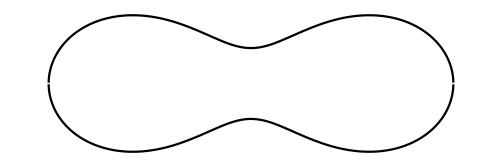

```mathematica
cassini=Plot[{Style[z[x],Black],Style[z2[x],Black]},{x,-3.8,3.8},AspectRatio->1/3,Axes->False]
```

```mathematica
Export["Cassini.svg",cassini]
```

Cassini.svg